```mathematica
H0=70;
H1[z_]:=H0√(Ωm(1+z)^3+Ωk(1+z)^2+ΩΛ)

H2[z_]:=FullSimplify[D[H1[z],z]]
h2=H2[z1]
```

(31.5 (1+z1)^2)/(√(0.7+0.3 (1+z1)^3))

```mathematica
H3[z_]:=FullSimplify[D[D[H1[z],z],z]]
h3=H3[z1]
```

((1+z1) (48.825+z1 (14.175+z1 (14.175+4.725 z1))))/((0.7+0.3 (1+z1)^3)^(3/2))

```mathematica
H4[z_]:=FullSimplify[D[D[D[H1[z],z],z],z]]
h4=H4[z1]
```

(-2.91375+z1 (-103.478+z1 (-109.856+z1 (-47.25+z1 (-10.6313+(-4.2525-0.70875 z1) z1)))))/(0.7+0.3 (1+z1)^3)^(5/2)

```mathematica
For Flat ΛCDM
```

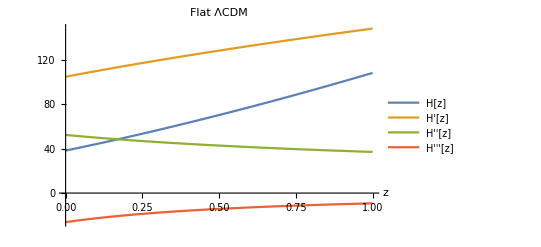

```mathematica
Ωm=0.3;
Ωk=0;
ΩΛ=0.7;
Plot[{H1[z1],h2,h3,h4},{z1,0.0001,1},PlotLabel->"Flat ΛCDM",PlotLegends->{"H[z]","H'[z]","H''[z]","H'''[z]"},AxesLabel->{"z"}]
```

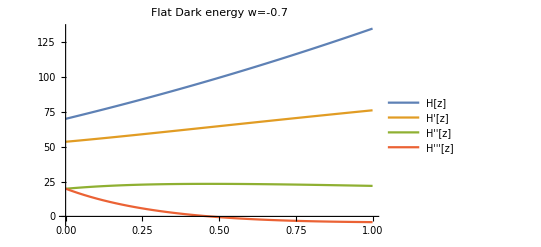

```mathematica
H1[z_]:=H0√(Ωm(1+z)^3+Ωk(1+z)^2+ΩΛ(1+z)^0.9)
H2[z_]:=FullSimplify[D[H1[z],z]]
h2=H2[z1];
H3[z_]:=FullSimplify[D[D[H1[z],z],z]]
h3=H3[z1];
H4[z_]:=FullSimplify[D[D[D[H1[z],z],z],z]]
h4=H4[z1];
Plot[{H1[z1],h2,h3,h4},{z1,0.0001,1},PlotLabel->"Flat Dark energy w=-0.7",PlotLegends->{"H[z]","H'[z]","H''[z]","H'''[z]"},AxesLabel->{"z"}]
```

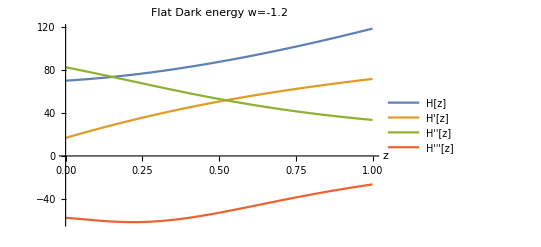

```mathematica
H1[z_]:=H0√(Ωm(1+z)^3+Ωk(1+z)^2+ΩΛ(1+z)^-0.6)
H2[z_]:=FullSimplify[D[H1[z],z]]
h2=H2[z1];
H3[z_]:=FullSimplify[D[D[H1[z],z],z]]
h3=H3[z1];
H4[z_]:=FullSimplify[D[D[D[H1[z],z],z],z]]
h4=H4[z1];
Plot[{H1[z1],h2,h3,h4},{z1,0.0001,1},PlotLabel->"Flat Dark energy w=-1.2",PlotLegends->{"H[z]","H'[z]","H''[z]","H'''[z]"},AxesLabel->{"z"}]
```

70

1

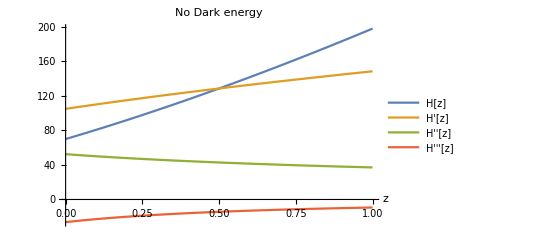

```mathematica
H0=70
Ωm=1
H1[z_]:=H0√(Ωm(1+z)^3)
H2[z_]:=FullSimplify[D[H1[z],z]]
h2=H2[z1];
H3[z_]:=FullSimplify[D[D[H1[z],z],z]]
h3=H3[z1];
H4[z_]:=FullSimplify[D[D[D[H1[z],z],z],z]]
h4=H4[z1];
Plot[{H1[z1],h2,h3,h4},{z1,0.0001,1},PlotLabel->"No Dark energy",PlotLegends->{"H[z]","H'[z]","H''[z]","H'''[z]"},AxesLabel->{"z"}]
```